-Graphics-

ψ= c1 s1 + c2 s2.
ψ* d0 ψ = c1* c2 s1* d0 s2+ c2* c1 s2* d0 s1

```mathematica
tmax=20;Ω0=1;ω0=30;df=2;
```

```mathematica
dp[N1_,N2_]:=√((2N2+1)(2N1+1))ThreeJSymbol[{N2,0},{1,0},{N1,0}]ThreeJSymbol[{N2,0},{1,0},{N1,0}]
```

```mathematica
H=({{0, Ω0 Cos[ω0/df t]}, {Ω0 Cos[ω0/df t], ω0}});
```

```mathematica
ψ[t_]={c1[t],c2[t]};init=ψ[0]=={1,0};SE=ⅈ ψ'[t]==H.ψ[t];
sols=NDSolve[{SE,init},{c1,c2},{t,tmax},PrecisionGoal->9,Method->"StiffnessSwitching"];{p1,p2}=Abs[#[t]/.sols]^2&/@{c1,c2};
```

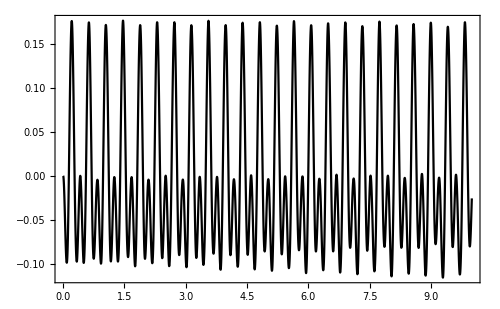

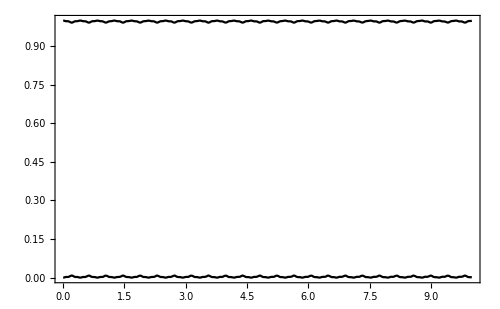

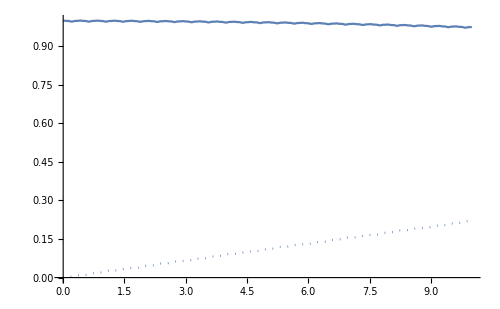

```mathematica
Plot[(c1[t]*c2[t]+c2[t]*c1[t])/.sols,{t,0,tmax}]
Plot[{(c1[t]*c1[t]),c2[t]*c2[t]*}/.sols,{t,0,tmax}]
ReImPlot[c1[t]/.sols,{t,0,tmax}]
```

```mathematica
Manipulate[Show[SphericalPlot3D[Evaluate[Abs[c1[t]SphericalHarmonicY[1,0,θ,ϕ]+c2[t]SphericalHarmonicY[0,0,θ,ϕ]]^2/.sols],{θ,0,π},{ϕ,0,2π},ViewPoint->{0, -2, 0},PlotStyle->{Red,Blue}[[(#+1)/2+1]],PlotRange->{-1,1}]&/@{-1,1},Graphics3D[Arrow[{{.2,0,0},{.2,0,((c1[t]*c2[t]+c2[t]*c1[t])/.sols)[[1]]}}]]],{t,0,tmax}]
```

```mathematica
SphericalPlot3D[Evaluate[Abs[c1[t]SphericalHarmonicY[1,0,θ,ϕ]+c2[t]SphericalHarmonicY[0,0,θ,ϕ]]^2/.sols/.t->1],{θ,0,π},{ϕ,0,2π}]
```

-Graphics3D-

```mathematica
(1/(√2)1/(√2)+1/(√2)1/(√2))
```

1

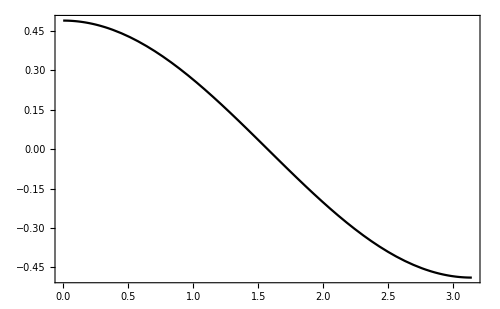

```mathematica
Plot[SphericalHarmonicY[1,0,θ,ϕ],{θ,0,π}]
```